```mathematica
shape[n_Integer]:=#[π(2Range[n]-1)/n]&/@{Cos,Sin}//Transpose;
(*--------------------------------------------------------------*)
coeff[polygon_List]:=With[{c=1+BitAnd[1,#]&,n=Length@polygon},
If[n==8,If[Count[polygon,1,2]==6,{.5,1.5},{1,2.+√2}],
{1,1.+(c[n]Sin[π/c[n]/n])^-1}]];
(*--------------------------------------------------------------*)
pointset[polygon_List,scale_:1]:=With[{n =10^6,r=coeff[polygon],
init=Map[RandomReal,Transpose[polygon]scale//All~Query~{Min,Max}]},
NestList[(RandomChoice[polygon]+r[[1]]#)/r[[2]]&,init,n]];
(*--------------------------------------------------------------*)
frames[polygon_List,steps_]:=Block[{c,g,p,r,start,mark,route,walk},
r=Range@Length[polygon];
mark={PointSize@Medium,Red,Point[#]}&;
p = ConstantArray[Graphics[],4steps];
start=Map[RandomReal,Transpose@polygon//All~Query~{Min,Max}];
Do[
c=RandomChoice@r;
route={start,polygon[[c]]};
walk={start,(#[[1]]start+polygon[[c]])/#[[2]]}&[coeff@polygon];
g={mark@start,Text[Style[c,Magenta,FontSize->36],Mean@polygon],
{Blue,Dashed,Line@route},{LightRed,Thin,Line@walk}};
MapIndexed[p[[4i+#2]]~Set~#1&,Graphics/@g];
start=Last@walk,
{i,0,steps-1}];
g={Graphics@GraphicsComplex[polygon,Point@r],
ListPlot[Labeled[polygon[[#]],Text[#],Bottom]&/@r]};
g~Join~p~Append~Graphics@mark@start];
(*--------------------------------------------------------------*)
index[n_Integer] := With[{t=n+1-Range[Mod[n-2,4]-1],
r=Select[Range[6,n],Mod[#,4]>1&]},
Range@Min[n,3]~Join~SortBy[r~Join~t,#~Mod~4&]];
```

```mathematica
triangle={{0,1},{-1,-1},{1.5,-1}};
animate[steps_]:=frames[triangle,steps];
```

```mathematica
With[{a=animate[15]},
With[{f=Show[a[[index@#]],ImageSize->Large]&/@Range[2,Length@a]},
Export["userwalk.gif",f,"DisplayDurations"->.5]]];
Directory[]
```

```mathematica
With[{gif=Import["https://i.stack.imgur.com/KRiRX.gif"]},
Animate[Show[gif[[n]],ImageSize->Large],{n,1,Length@gif,1},
AnimationRunning->False,AnimationRate->.7]]
```

```mathematica
With[{a=animate[50]},
Animate[Show[a[[index@n]],ImageSize->Large],{n,2,Length@a,1},
AnimationRunning->False,AnimationRate->.7]]
```

#### Implementation of the Chaos Game

```mathematica
set=pointset[triangle];
```

```mathematica
game[steps_Integer] := Module[{p1, p2, p3,size},
size=(1+15Log[#,#/steps]^1.35)&[Length@set]/2.1;
p1={PointSize[Large],Darker@Green,Point[triangle]};
p2=Text[Style["steps" steps,Blue,FontSize->20],{1.2,.9}];
p3={AbsolutePointSize@size,Red,Point@set[[1;;steps]]};
Show[Graphics/@{p1, p2, p3},ImageSize->Large]]
```

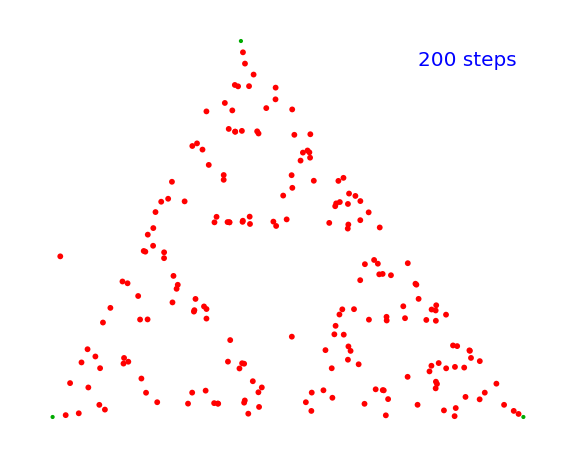

```mathematica
game[200]
```

```mathematica
Manipulate[game@Round[1.304^n],{n,2,52,1}]
```

```mathematica
With[{p=Join[1.304^Range[2,52],Length@set-{2,1}]},
With[{frames=game@Round[#]&/@p},
Export["game.gif",frames,"DisplayDurations"->.4]]];
```

#### Sierpiński carpet

```mathematica
set=pointset@DeleteCases[Tuples[{-1,0,1},{2}],{0,0}];
```

```mathematica
carpet[n_Integer]:= Module[{ p1, p2,size},
size=(1+15Log[#,#/n]^1.13)&[Length@set]/2.1;
p1=Text[Style["steps" n, Darker@Green,FontSize -> 18],{0,0}];
p2={AbsolutePointSize@size,Blue,Point@set[[1;;n]]};
Show[Graphics/@{p1, p2},PlotRange->1.05, ImageSize -> Large]]
```

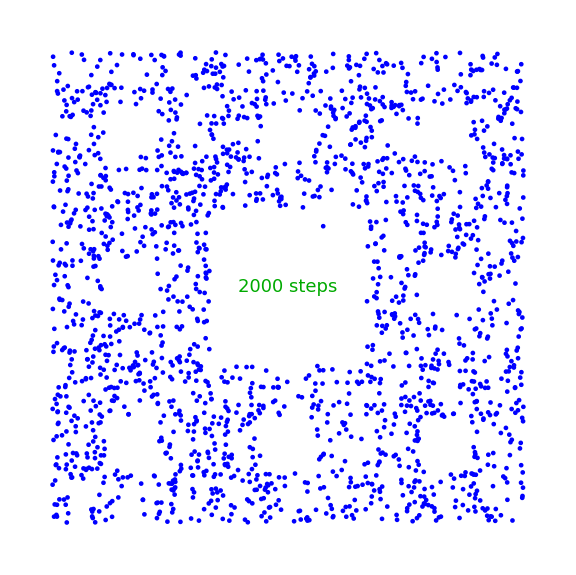

```mathematica
carpet[2000]
```

```mathematica
With[{p=Join[1.304^Range[2,52],Length@set-Range[9,1,-1]]},
With[{frames=carpet@Round[#]&/@p},
Export["carpet.gif",frames,"DisplayDurations"->.4]]];
```

#### Pentagonal Snowflake

```mathematica
set=pointset@shape[5];
```

```mathematica
flake5[n_Integer]:= Module[{r, p1, p2,size},
size=(1+15Log[#,#/n]^1.13)&[Length@set]/2.1;
r=Transpose@shape[5]/GoldenRatio//All~Query~{Min,Max};
p1=Text[Style["steps" n, Darker@Green,FontSize -> 18],{0,0}];
p2={AbsolutePointSize@size,Blue,Point@set[[1;;n]]};
Show[Graphics[#,PlotRange->1.05r]&/@{p1, p2},ImageSize -> Large]]
```

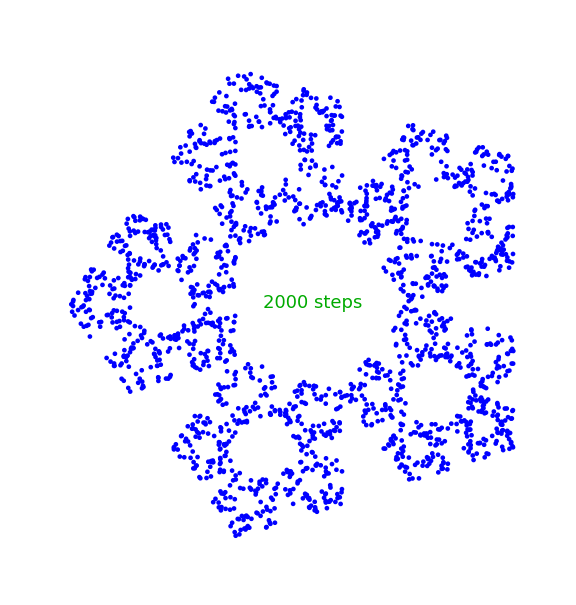

```mathematica
flake5[2000]
```

```mathematica
With[{p=Join[1.304^Range[2,52],Length@set-{2,1}]},
With[{frames=flake5@Round[#]&/@p},
Export["flake5.gif",frames,"DisplayDurations"->.4]]];
```

#### Hexagonal Snowflake

```mathematica
set=pointset@shape[6];
```

```mathematica
flake6[n_Integer]:= Module[{r, p1, p2,size},
size=(1+15Log[#,#/n]^1.13)&[Length@set]/2.1;
r=Transpose@shape[6]/2//All~Query~{Min,Max};
p1=Text[Style["steps" n, Darker@Green,FontSize -> 18],{0,0}];
p2={AbsolutePointSize@size,Blue,Point@set[[1;;n]]};
Show[Graphics[#,PlotRange->1.05r]&/@{p1, p2},ImageSize -> Large]]
```

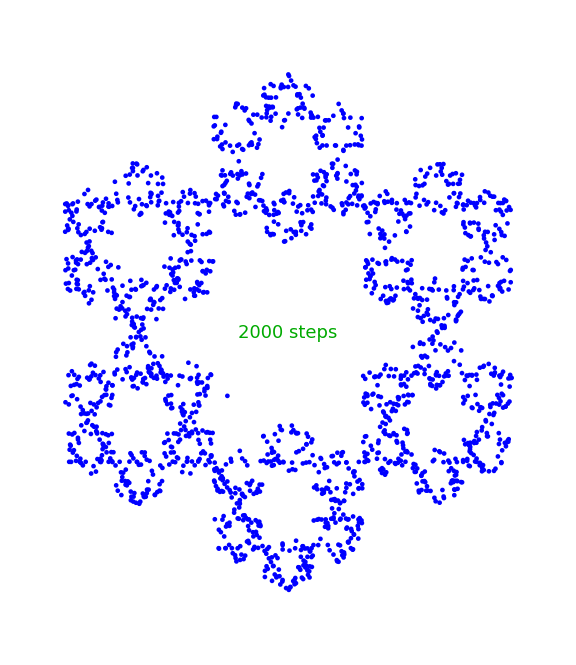

```mathematica
flake6[2000]
```

```mathematica
With[{p=Join[1.304^Range[2,52],Length@set-{2,1}]},
With[{frames=flake6@Round[#]&/@p},
Export["flake6.gif",frames,"DisplayDurations"->.4]]];
```

#### Fractal generation

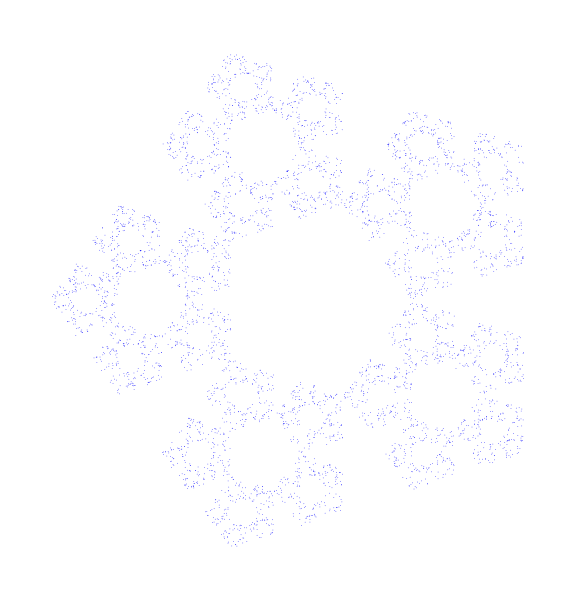

```mathematica
set=pointset[shape[5],1/2];
Show[Graphics@{AbsolutePointSize[1/2],Blue,Point@set[[1;;5000]]},ImageSize -> Large]
```

```mathematica
Do[set=pointset[shape[n],1/2];
Export["fractal"<>ToString[n]<>".png",
Show[Graphics@{AbsolutePointSize[1/2],Blue,Point@set},ImageSize -> 2000]],{n,3,11}];
```